```mathematica
(*Initialisation - Run first*)
SetEnvironment["OMP_NUM_THREADS"->"8"]
(*Replace the following with the appropriate pathways for your device*)
Import["/Users/questuser/Documents/QuESTlink/Link/QuESTlink.m"] (*QuESTlink load*)
CreateLocalQuESTEnv["/Users/questuser/Documents/Kathryn/quest_link"]; (*Creating QuEST environment*)
Import["/Users/questuser/Documents/Kathryn/RydbergGerardCZDCSWAP.wl"]; 
userconfig=<|
NQubits-> 9,
QubitLocations->Association[#1->#2&@@@Transpose@{Range[0,8],{{1,1,0},{0,0,0},{1,0,0},{2,0,0},{0,1,0},{2,1,0},{0,2,0},{1,2,0},{2,2,0}}}](*,{1,2,0}}}]*),
(* blockade radius in μm*)
BlockadeRadius->Sqrt[2],
(*BlockadeRadius->3,*)
(* inter-atomic separation in μm. This will be the unit of the lattice given in qubitLocations *)
UnitLattice->1,
(* T1=τvac/nqubits in μs *)
VacuumLifeTime->4*10^6,
(* the γ noise on theq initialization *)
LeakProbInit->0.007,
(* duration on the initialization *)
DurInit->300,
(* measurement induces atom loss afterward *)
FidMeas-> 98,
DurMeas-> 2*10^4,
(* the increasing chance of atom loss due to measurement, in percent *)
AtomLossMeas-> 0,
(* mostly used in the single qubit noise, unit μs. It's presumed that Subscript[T, 2]^* has been echoed out to Subscript[T, 2] *)
T2->1.49*10^6,
(* leak probability of implementing multi-qubit gates *)
LeakProbCZ-> <|01-> 0.001,11->0.001 |>,
(* Rabi frequency, MHz *)
Ω->1,
(* fidelity of swap operation *)
FidSWAP->99.7
|>;
RydDev=CreateRydbergDevice[userconfig];
RydDev[Gates][[All,1]]
RydDev[InitLocations]
data=data=Import["/Users/questuser/Documents/Kathryn/BV3to9Q.csv"]; (*Imported gates from Qiskit*)
data[[5]];
d=data[[5]][[3;;data[[2,1]]+2]];
Length[data]
Fraction[a_,b_]:=a/b
(*Defining QuEST's Rydberg Blockade Check in a permanent function such that it can be used without constantly editing the code*)
qubitLocs=userconfig[QubitLocations];
distloc[q1_,q2_]:=Norm[qubitLocs[q1]-qubitLocs[q2],2]*userconfig[UnitLattice];
blockadeCheck[q_List]:=And@@((distloc@@#<= userconfig[BlockadeRadius])&/@Subsets[Flatten[q],{2}]);
```

{Init_q$_Integer,Wait_qubits$__[dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},M_q$_Integer,SRot_q$_Integer[ϕ$_,Δ$_,tg$_],H_q$_Integer,Rx_q$_Integer[θ$_],Ry_q$_Integer[θ$_],Rz_q$_Integer[θ$_],SWAP_(q1$_Integer,q2$_Integer),SWAPLoc_(q1$_Integer,q2$_Integer),ShiftLoc_q$__[v$_]/;LegitShift[Flatten[{q$}],qubitLocs$5208116,v$],CZ_(p$_Integer,q$_Integer)[ϕ$_]/;blockadeCheck$5208116[{p$,q$}],C_c$_[Z_t$__]/;blockadeCheck$5208116[{c$,t$}],C_c$_[Z_t$__[θ$_]]/;blockadeCheck$5208116[{c$,t$}],C_c$__[Z_t$_]/;blockadeCheck$5208116[{c$,t$}],C_c$__[Z_t$_[θ$_]]}

-Graphics3D-

508

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

ExtractCircuit::error: Invalid arguments. See ?ExtractCircuit

CalcCircuitMatrix::error: Circuit contained an unrecognised or unsupported gate: $Failed

$Failed

{Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}

(-1 | 0 | 0 | 0
0 | 0 | 0 | -1
0 | 0 | -1 | 0
0 | -1 | 0 | 0)

{Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_1[π],Deph_1[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(1,0)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π],Deph_0[1.67785×10^-7],Ry_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}

(-1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -1 | 0 | 0
0 | 0 | -1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -1
0 | 0 | 0 | 0 | -1 | 0 | 0 | 0
0 | -1 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -1 | 0
0 | 0 | 0 | -1 | 0 | 0 | 0 | 0)

{Rx_0[-π],Deph_0[1.67785×10^-7],Ry_2[π/2],Deph_2[8.38926×10^-8],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_2[π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[1.05422×10^-6],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,0)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π],Deph_0[1.67785×10^-7],Ry_2[π/2],Deph_2[8.38926×10^-8],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}

(1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0)

{Rx_0[-π],Deph_0[1.67785×10^-7],Ry_1[π/2],Deph_1[8.38926×10^-8],Ry_2[π/2],Deph_2[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_1[π],Deph_1[1.67785×10^-7],Rx_2[π],Deph_2[1.67785×10^-7],Deph_0[1.05422×10^-6],Deph_1[0.],Deph_2[0.],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(2,0)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[4.36241×10^-7],Deph_2[0.],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π],Deph_0[1.67785×10^-7],Ry_2[π/2],Deph_2[8.38926×10^-8],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[5.27113×10^-7],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],KrausNonTP_(1,0)[{{{1,0,0,0},{0,-0.998564+0.0294972 ⅈ,0,0},{0,0,-0.998564+0.0294972 ⅈ,0},{0,0,0,-0.9986}}}],Deph_0[0.],Deph_1[0.],Deph_2[4.36241×10^-7],Deph_3[4.36241×10^-7],Deph_4[4.36241×10^-7],Deph_5[4.36241×10^-7],Deph_6[4.36241×10^-7],Deph_7[4.36241×10^-7],Deph_8[4.36241×10^-7],Ry_0[-π],Deph_0[1.67785×10^-7],Ry_1[π/2],Deph_1[8.38926×10^-8],Deph_0[0.],Deph_1[5.27113×10^-7],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6],Rx_0[-π],Deph_0[1.67785×10^-7],Deph_0[0.],Deph_1[1.05422×10^-6],Deph_2[1.05422×10^-6],Deph_3[1.05422×10^-6],Deph_4[1.05422×10^-6],Deph_5[1.05422×10^-6],Deph_6[1.05422×10^-6],Deph_7[1.05422×10^-6],Deph_8[1.05422×10^-6]}

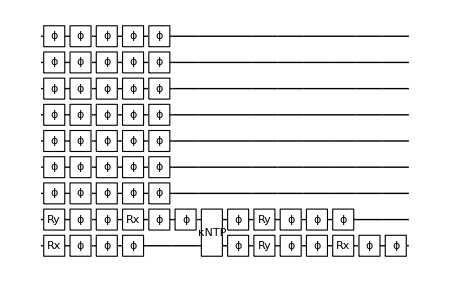
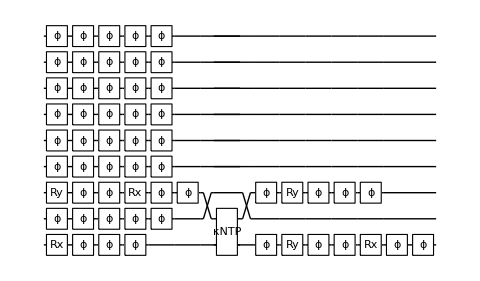
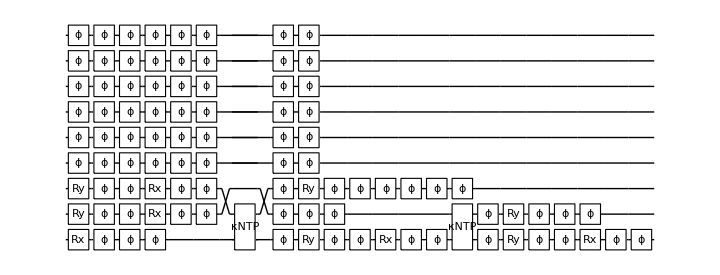
{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
CircuitTranslator[DataSet_]:=Table[CircSplit=DataSet[[i,3;;DataSet[[i,1]]+2]];
(*Print[CircSplit];*)
Table[GateSplit=StringSplit[CircSplit[[j]],", ["];
GateName=StringTrim[StringTrim[GateSplit[[1]],"["],"'"];
GateQubits=IntegerPart[ToExpression[StringSplit[StringTrim[GateSplit[[2]],"]"],","]]];
GateParameters=If[StringContainsQ[GateName,"C"],Pi,Pi*ToExpression[StringReplace[StringTrim[GateSplit[[3]],"]]"],{"("->"[",")"->"]"}]]];
If[Length[GateQubits]==2,Subscript[ToExpression[GateName], GateQubits[[1]],GateQubits[[2]]][GateParameters],Subscript[ToExpression[GateName], GateQubits[[1]]][GateParameters]],{j,1,DataSet[[i,1]]}]
,{i,1,Length[DataSet]}]
(*a=data[[2;;Length[data]]][[1]][[3;;9]]*)
Table[Print[MatrixForm[CalcCircuitMatrix[ExtractCircuit[GetCircuitSchedule[CircuitTranslator[data][[i]][[2;;]],RydDev,ReplaceAliases->True]]]]];CircA=ExtractCircuit[InsertCircuitNoise[CircuitTranslator[data][[i]],RydDev,ReplaceAliases->True]];Print[CircA];DrawCircuit[CircA],{i,1,4}]
```

```mathematica
{Subscript[Init, q$_Integer],Subscript[Wait, qubits$__][dur$_]/;Complement[Flatten[{qubits$}],Range[0,userconfig[NQubits]-1]]==={},Subscript[M, q$_Integer],Subscript[SRot, q$_Integer][ϕ$_,Δ$_,tg$_],Subscript[H, q$_Integer],Subscript[Rx, q$_Integer][θ$_],Subscript[Ry, q$_Integer][θ$_],Subscript[Rz, q$_Integer][θ$_],Subscript[SWAP, q1$_Integer,q2$_Integer],Subscript[SWAPLoc, q1$_Integer,q2$_Integer],Subscript[ShiftLoc, q$__][v$_]/;LegitShift[Flatten[{q$}],qubitLocs$1852814,v$],Subscript[CZ, p$_Integer,q$_Integer][ϕ$_]/;blockadeCheck$1852814[{p$,q$}],Subscript[C, c$_][Subscript[Z, t$__]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$_][Subscript[Z, t$__][θ$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_]]/;blockadeCheck$1852814[{c$,t$}],Subscript[C, c$__][Subscript[Z, t$_][θ$_]]}
```

```mathematica
KetList[NQ_]:=Table[ToExpression@StringSplit[IntegerString[i,2,NQ],""],{i,0,2^NQ-1,1}]
KetList[2]
Length[%]
```

{{0,0},{0,1},{1,0},{1,1}}

4

```mathematica
{"0000","0001","0010","0011","0100","0101","0110","0111","1000","1001","1010","1011","1100","1101","1110","1111"}
```

16

```mathematica
percent2infidel[num_]:=Module[{},Assert[0<=num<=100,"number is in percent"];1-0.01 num];
MeasErrors[QubitList_]:=Table[Subscript[Depol, QubitList[[i]]][percent2infidel[userconfig[FidMeas]]],{i,1,Length[QubitList]}]
MeasBuilder[QuReg_,QubitList_]:=Table[CalcProbOfOutcome[QuReg,QubitList[[i]],0],{i,1,Length[QubitList]}]
Circs=CircuitTranslator[data];
(*Gate Errors Only*)

(*BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[InitZeroState[ρ];
ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Circs[[i]],RydDev,ReplaceAliases->True]]];Res=CalcProbOfAllOutcomes[ρ,Range[1,Nq-1]]
,{i,1,Length[Circs]}]*)
(*Initialisation and Gate Errors*)
(*BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[SetQuregMatrix[ρ,RandomMixState[9]];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,userconfig[NQubits]-1}],Circs[[i]]],RydDev,ReplaceAliases->True]]];Res=CalcProbOfAllOutcomes[ρ,Range[1,Nq-1]]
,{i,1,Length[Circs]}]*)

(*Gate, Initialisation and Measurement Errors*)
BVCircuitApplier[Circs_,ρ_,Nq_]:= Table[SetQuregMatrix[ρ,RandomMixState[userconfig[NQubits]]];ApplyCircuit[ρ,ExtractCircuit[InsertCircuitNoise[Join[Table[Subscript[Init, j],{j,0,userconfig[NQubits]-1}],Circs[[i]]],RydDev,ReplaceAliases->True]]];
ApplyCircuit[ρ,MeasErrors[Reverse[Range[1,Nq-1]]]];
P0s=MeasBuilder[ρ,Reverse[Range[1,Nq-1]]]; P1s=ConstantArray[1,Length[P0s]]-P0s;Pops=Table[PSeed=KetList[Nq-1][[j]];ProbSeed=P1s*PSeed +P0s*(PSeed/.{0->1,1->0});
Times@@ProbSeed,{j,1,2^(Nq-1)}];
{Pops,Max[Flatten[Position[Pops,RankedMax[Pops,2]]]]},
{i,1,Length[Circs]}]
ρ=CreateDensityQureg[9];
i=1
Table[Print[Nq];Probs=BVCircuitApplier[Circs[[i;;i+2^(Nq-1)-1]],ρ,Nq];i=i+2^(Nq-1);Probs,{Nq,3,9}]

DestroyAllQuregs[];
```

1

3

4

5

6

7

8

9

```mathematica
?CalcProbOfAllOutcomes
```

```mathematica
?QuEST`*
```

```mathematica
BVDataNoInitNoMeas=;
```

```mathematica
BVDataInitNoMeas=;
```

```mathematica
BVDataInitMeas=;
```

```mathematica
BVDataNoInitNoMeas[[1,1]]
```

{1.,0.,0.,0.}

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

{{2,0.997384±0.00213486},{3,0.996078±0.00171028},{4,0.994773±0.00134797},{5,0.993469±0.00104747},{6,0.992166±0.000804236},{7,0.990864±0.000611315},{8,0.989563±0.000460821}}

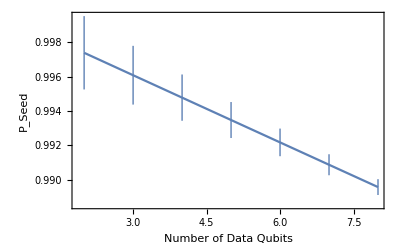

```mathematica
AvgProbs=Table[Res=BVDataNoInitNoMeas[[i]];x=Range[0,2^(i+1)];
y=Range[0,2^(i+1)];
Print[Histogram3D[{{0,0}},{{x},{y}},Res&,AxesLabel->{"Input Seed","Resultant State","Probability"},ColorFunction->Function[{height},ColorData["Pastel"][height]]]];μ=(Total[Diagonal[Res]]/Length[Res]); {i+1,μ±2*StandardDeviation[Diagonal[Res]]/Sqrt[2^(i+1)]},{i,1,7}]
ListLinePlot[AvgProbs,Frame->True,FrameLabel->{Style["Number of Data Qubits",16],Style["P_Seed",16]}]
```

-Graphics3D-

-Graphics3D-

-Graphics3D-

«4 more identical outputs»

{{2,0.91432±0.0478092},{3,0.872724±0.036695},{4,0.832035±0.0276762},{5,0.792305±0.020556},{6,0.75358±0.0150675},{7,0.715901±0.0109213},{8,0.679301±0.00784113}}

-Graphics-

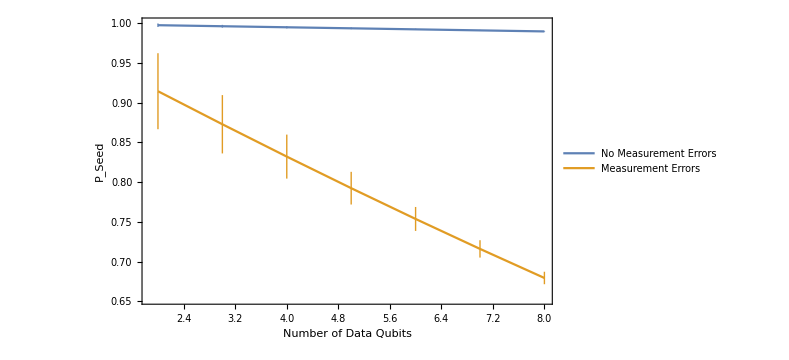

-Graphics3D-

-Graphics3D-

-Graphics3D-

«3 more identical outputs»

{{2,0.976585±0.00209034},{3,0.968479±0.0016629},{4,0.96044±0.00130145},{5,0.952466±0.00100424},{6,0.944559±0.000765646},{7,0.936716±0.000577909},{8,0.928938±0.000432589}}

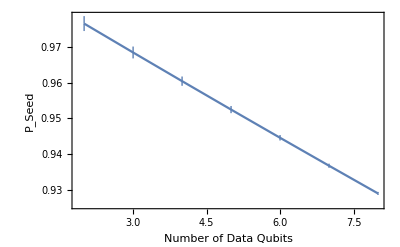

```mathematica
AvgProbsMeas=Table[Res=BVDataInitMeas[[i]];x=Range[0,2^(i+1)];
y=Range[0,2^(i+1)];
Print[Histogram3D[{{0,0}},{{x},{y}},Res&,AxesLabel->{"Input Seed","Resultant State","Probability"},ColorFunction->Function[{height},ColorData["Pastel"][height]]]];μ=(Total[Diagonal[Res]]/Length[Res]); {i+1,μ±2*StandardDeviation[Diagonal[Res]]/Sqrt[2^(i+1)]},{i,1,7}]
ListLinePlot[AvgProbs,Frame->True,FrameLabel->{Style["Number of Data Qubits",16],Style["P_Seed",16]}]
ListLinePlot[{AvgProbs,AvgProbsMeas},Frame->True,FrameLabel->{Style["Number of Data Qubits",16],Style["P_Seed",16]},PlotLegends->{"No Measurement Errors","Measurement Errors"}]
```

```mathematica
?Deph
```

```mathematica
?RandomMixState
```

```mathematica
?Depol
```

```mathematica
?QuEST`*
```

```mathematica
MeasErrors[QubitList_]:=Table[Subscript[Depol, QubitList[[i]]][Min[1-3*0.001*98-1,0.75]],{i,1,Length[QubitList]}]
MeasBuilder[QuReg_,QubitList_]:=Module[{P0};ApplyCircuit[QuReg,MeasErrors[QubitList]];P0=Table[CalcProbOfOutcome[QuReg,QubitList[[i]],0],{i,1,Length[QubitList]}],{P0,1-P0}]
```